```mathematica
Clear["Global`*"]
```

# Taylor Expansion

## Cory Aitchison - January 2022

Repeating the Taylor expansion except only including up to the fifth order cosh terms.

## Set Up

### Miscellaneous

```mathematica
CC[x_]:=Cos[σ x] / Cosh[σ x];
SS[x_]:=Sin[σ x] / Sinh[σ x];
LDE[f_]:=D[f[x],{x,4}] + 4 σ^4 f[x] ;
NDE[f_]:=Γ f[x]^3;
letters = {c, d, e, f, g, h, i, j, k};
```

### Ansatz

```mathematica
u[n_]:=x|->Sum[letters[[n]][i]CC[x]^((2n+1)-i) SS[x]^(i), {i, 0, 2n+1}];
u[0] := x |->A CC[x] + B SS[x];
```

```mathematica
<<"/Users/cory/Sync/USYD/Denison/Mathematica/PQSHelper.wl"
```

### Solutions

```mathematica
SubAnswers[eq_, n_] := SubAnswers[eq /. answer[n-1], n-1];
SubAnswers[eq_, 1] := eq;

GetEquation[n_]:= LDE[x |-> Sum[u[k][x], {k, 0, n}]] + NDE[x |-> Sum[u[k][x], {k, 0, n-1}]];
GetSolution[n_] := AnalyticSolve[SubAnswers[GetEquation[n], n], n, x, σ, letters[[n]]] // FullSimplify;

GetLinear[ans_] := Coefficient[(Last /@List @@@ ans)/. B->0 ,A, 1]A + Coefficient[(Last /@List @@@ ans)/. A->0 ,B, 1]B;
ShowLinear[n_]:=(x |-> PadRight[x, 2 + 2n,  _])/@GetLinear/@ (answer[#]&/@Range[1,n]) // Transpose// MatrixForm ;

ShowValues[n_] := (x |-> PadRight[x, 2 + 2n, _])/@((answer[#]/. param /. estimates)&/@Range[1,n])//Transpose//MatrixForm;

FinalFunction[n_] := SubAnswers[Sum[u[k][x], {k, 0, n}], n+1]/.param /. estimates;
FinalFunction[0] := u[0][x] /. param /. estimates;
```

### Numerical Values

```mathematica
param = {σ-> 6^(1/4), Γ -> -24};
estimates = {A -> 0.445408, B -> 1.02817};
```

```mathematica
DumpGet["/Users/cory/Sync/USYD/Denison/Mathematica/answerSave.mx"]
```

## Taylor Expansions

```mathematica
f[x_]:= SubAnswers[u[1][x] + u[0][x], 2];
de[f_]:=x|->f''''[x] + 4 σ^4 f[x] + Γ f[x]^3;
htrigident = {
cosh^k_-> (1+sinh^2)^(Floor[k/2]) cosh^(Mod[k,2])
};
trigident = {
Cos[x σ]^k_-> (1-Sin[x σ]^2)^(Floor[k/2]) Cos[x σ]^(Mod[k,2]) 
};
eq2 = (de[f][x] /. {Csch[_] -> 1/sinh, Sech[_] -> 1/cosh, Coth[_] -> cosh / sinh,Tanh[_] -> sinh/cosh})//Together;
order = ((Length[CoefficientList[#, cosh]] - 1) + (Length[CoefficientList[#, sinh]] - 1))&@Denominator[eq2];
list1 = CoefficientList[Expand[Numerator[eq2] //. htrigident], {sinh, cosh}];
list2 = {
		list1[[order - 5, 2]],
		list1[[order - 4, 1]]
	};
fifthorder = list2 . {Sinh[x σ]^(order - 6) Cosh[x σ], Sinh[x σ]^(order-5)} /Denominator[eq2]  /. {cosh -> Cosh[x σ], sinh ->Sinh[x σ]};
```

```mathematica
Series[fifthorder /. param ,x -> 0]
```

1/(20 2^(1/4))3 3^(3/4) (-16000 6^(1/4) A-2220 6^(1/4) A^3+21 6^(1/4) A^5-14400 6^(1/4) B-1800 6^(1/4) A^2 B-21 6^(1/4) A^4 B-2940 6^(1/4) A B^2-45 6^(1/4) A^3 B^2-1800 6^(1/4) B^3-81 6^(1/4) A^2 B^3-54 6^(1/4) A B^4) x^4+O[x]^5

```mathematica
Solve[Series[fifthorder == 0 /. param , {x,0,6}], {A, B}, Assumptions->{{A, B}∈ Reals}] // N
```

{{A→0.,B→0.},{A→-11.5083,B→13.8769},{A→-1.80377,B→2.36266},{A→1.80377,B→-2.36266},{A→11.5083,B→-13.8769}}

So when we only leave in the fifth order sech terms (note the third order etc. are zero by construction), we get a Taylor series where the leading term is x^4.

```mathematica
seventhorder = {list1[[order-7,2]],list1[[order-6,1]]} . {Sinh[x σ]^(order-8) Cosh[x σ], Sinh[x σ]^(order - 7)} / Denominator[eq2]  /. {cosh -> Cosh[x σ], sinh ->Sinh[x σ]};
```

```mathematica
Series[fifthorder + seventhorder == 0 /. param, {x, 0, 6}] /. {A-> 1, B->1} // N
```

-14248.7 (x+0.)^2+174489. (x+0.)^4-1.1132×10^6 (x+0.)^6+O[x+0.]^7==0.

When including the seventh order terms, we get x^2 coefficients

```mathematica
Solve[Series[fifthorder + seventhorder == 0 /. param , {x,0,4}], {A, B}, Assumptions->{{A, B}∈ Reals}] // N
```

{{A→0.,B→0.},{A→-19.0044,B→-289112.},{A→-8.99307,B→-0.911622},{A→-1.87402,B→2.32709},{A→1.87402,B→-2.32709},{A→8.99307,B→0.911622},{A→19.0044,B→289112.}}

```mathematica
nthorder[n_]:= {list1[[order-n,2]],list1[[order-n+1,1]]} . {Sinh[x σ]^(order-n-1) Cosh[x σ], Sinh[x σ]^(order - n)} / Denominator[eq2]  /. {cosh -> Cosh[x σ], sinh ->Sinh[x σ]};
```

```mathematica
Series[fifthorder + seventhorder +nthorder[9]+ nthorder[11]== 0 /. param, {x, 0, 6}] /. estimates // N
```

-1191.26/(x+0.)^2+18916.6-153948. (x+0.)^2+858562. (x+0.)^4-3.69138×10^6 (x+0.)^6+O[x+0.]^7==0.

As we add higher terms, it diverges at 0??

```mathematica
Series[de[f][x], x->0]
```

1/(786432000 σ^12)(375 A^9 Γ^4-2025 A^8 B Γ^4+5670 A^7 B^2 Γ^4-12402 A^6 B^3 Γ^4+20736 A^5 B^4 Γ^4-26568 A^4 B^5 Γ^4+28746 A^3 B^6 Γ^4-23166 A^2 B^7 Γ^4+13689 A B^8 Γ^4-6591 B^9 Γ^4+216000 A^7 Γ^3 σ^4-705600 A^6 B Γ^3 σ^4+1218240 A^5 B^2 Γ^3 σ^4-2030400 A^4 B^3 Γ^3 σ^4+1880640 A^3 B^4 Γ^3 σ^4-1114560 A^2 B^5 Γ^3 σ^4+786240 A B^6 Γ^3 σ^4+486720 B^7 Γ^3 σ^4+41472000 A^5 Γ^2 σ^8-47001600 A^4 B Γ^2 σ^8+29491200 A^3 B^2 Γ^2 σ^8-66355200 A^2 B^3 Γ^2 σ^8-63590400 A B^4 Γ^2 σ^8-11980800 B^5 Γ^2 σ^8+2850816000 A^3 Γ σ^12+2025062400 A^2 B Γ σ^12+1081344000 A B^2 Γ σ^12-1002700800 B^3 Γ σ^12+41943040000 A σ^16-12582912000 B σ^16)+O[x]^2

```mathematica
Limit[de[f][x], x -> 0]
```

1/(786432000 σ^12)(375 A^9 Γ^4-2025 A^8 B Γ^4+270 A^7 Γ^3 (21 B^2 Γ+800 σ^4)-18 A^6 B Γ^3 (689 B^2 Γ+39200 σ^4)+5184 A^5 Γ^2 (4 B^4 Γ^2+235 B^2 Γ σ^4+8000 σ^8)-216 A^4 B Γ^2 (123 B^4 Γ^2+9400 B^2 Γ σ^4+217600 σ^8)-6 A^2 B Γ (3861 B^6 Γ^3+185760 B^4 Γ^2 σ^4+11059200 B^2 Γ σ^8-337510400 σ^12)+6 A^3 Γ (4791 B^6 Γ^3+313440 B^4 Γ^2 σ^4+4915200 B^2 Γ σ^8+475136000 σ^12)+A (13689 B^8 Γ^4+786240 B^6 Γ^3 σ^4-63590400 B^4 Γ^2 σ^8+1081344000 B^2 Γ σ^12+41943040000 σ^16)-3 (2197 B^9 Γ^4-162240 B^7 Γ^3 σ^4+3993600 B^5 Γ^2 σ^8+334233600 B^3 Γ σ^12+4194304000 B σ^16))

So the Series[] is defined, but the value isn’t?

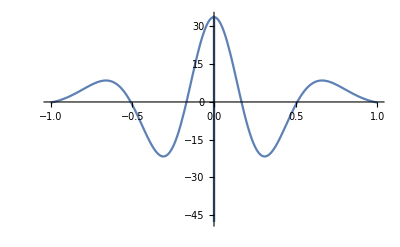

```mathematica
Plot[de[f][x] /. param /. estimates, {x, -1, 1}]
```

```mathematica
Manipulate[Plot[de[f][x] /. param /. {A->Ξ Cos[θ]^2, B->Ξ Sin[θ]^2}, {x, -1, 1}], {Ξ, 0, 2}, {θ, 0.6, 1.3}]
```

```mathematica
ArcTan[Sqrt[0.898534/0.242423]]
```

1.09173

```mathematica
Limit[de[f][x], x->0] /. param /. {A->0.24242264239512362,B->0.8985343791605391}
```

-4.91239×10^-17

```mathematica
A+B/.{A->0.24242264239512362,B->0.8985343791605391}
```

1.14096

```mathematica
list1 /. trigident /. param /. {A->1, B->1} // Expand
```

{{0,241864704000 Sin[6^(1/4) x]^9},{-790091366400 Cos[6^(1/4) x] Sin[6^(1/4) x]^8,0},{0,-275188285440000 Sin[6^(1/4) x]^3-929477099520 Sin[6^(1/4) x]^7-682954260480 Sin[6^(1/4) x]^9},{650259726336000 Cos[6^(1/4) x] Sin[6^(1/4) x]^2+151040360448 Cos[6^(1/4) x] Sin[6^(1/4) x]^6-272868507648 Cos[6^(1/4) x] Sin[6^(1/4) x]^8,0},{0,-444785806540800 Sin[6^(1/4) x]-657598080614400 Sin[6^(1/4) x]^3+9772241780736 Sin[6^(1/4) x]^5-9625840975872 Sin[6^(1/4) x]^7+158169563136 Sin[6^(1/4) x]^9},{69714365644800 Cos[6^(1/4) x]+2971625796403200 Cos[6^(1/4) x] Sin[6^(1/4) x]^2+8063972278272 Cos[6^(1/4) x] Sin[6^(1/4) x]^4+7596422922240 Cos[6^(1/4) x] Sin[6^(1/4) x]^6+110776025088 Cos[6^(1/4) x] Sin[6^(1/4) x]^8,0},{0,-1905933680640000 Sin[6^(1/4) x]+307008369524736 Sin[6^(1/4) x]^3+20573397909504 Sin[6^(1/4) x]^5-3429534007296 Sin[6^(1/4) x]^7-12655263744 Sin[6^(1/4) x]^9},{321936320102400 Cos[6^(1/4) x]+5172176665903104 Cos[6^(1/4) x] Sin[6^(1/4) x]^2+49621623570432 Cos[6^(1/4) x] Sin[6^(1/4) x]^4+4874017701888 Cos[6^(1/4) x] Sin[6^(1/4) x]^6-10956570624 Cos[6^(1/4) x] Sin[6^(1/4) x]^8,0},{0,-3176022842966016 Sin[6^(1/4) x]+2275072993198080 Sin[6^(1/4) x]^3+35926786179072 Sin[6^(1/4) x]^5+842127114240 Sin[6^(1/4) x]^7+339738624 Sin[6^(1/4) x]^9},{669320132788224 Cos[6^(1/4) x]+3910132580548608 Cos[6^(1/4) x] Sin[6^(1/4) x]^2+53985762607104 Cos[6^(1/4) x] Sin[6^(1/4) x]^4-949994127360 Cos[6^(1/4) x] Sin[6^(1/4) x]^6+339738624 Cos[6^(1/4) x] Sin[6^(1/4) x]^8,0},{0,-2966956513689600 Sin[6^(1/4) x]+2944236917882880 Sin[6^(1/4) x]^3+16918983475200 Sin[6^(1/4) x]^5-40768634880 Sin[6^(1/4) x]^7},{331947143331840 Cos[6^(1/4) x]+1247043743907840 Cos[6^(1/4) x] Sin[6^(1/4) x]^2+13168269066240 Cos[6^(1/4) x] Sin[6^(1/4) x]^4+40768634880 Cos[6^(1/4) x] Sin[6^(1/4) x]^6,0},{0,-1250985561292800 Sin[6^(1/4) x]+1354198155264000 Sin[6^(1/4) x]^3-1630745395200 Sin[6^(1/4) x]^5},{-85546185523200 Cos[6^(1/4) x]+189302361292800 Cos[6^(1/4) x] Sin[6^(1/4) x]^2-1630745395200 Cos[6^(1/4) x] Sin[6^(1/4) x]^4,0},{0,0},{0,0}}

The fifth order term is of the form sinh^4/cosh^9, then the 7th is sinh^2/cosh^9, and the 9th is 1/cosh^9. Therefore, we get less 1/sinh (which is order 1/x) terms, which brings the taylor expansion from x^4 -> x^2 -> 1. With the addition of the 11th order term we get 1/sinh^2cosh^9, which gives 1/x^2 expansions.

Therefore we get a strong divergence and contribution at 0 from these higher order terms.

This makes sense! The functions are designed so that they are satisfied up to a certain order of 1/cosh. This assumption is close to the true function when we are in the tails, so 1/cosh^5 -> 0. But at the peak, the 1/cosh^5, 1/sinh^10 terms are dominant and cannot be ignored. So we are mixing up two “orders” - the 1/cosh which is expanding in the tails, and x which is expanding at the peak. We cannot expect the tail approximation to give a close fit at the peak (as we observed in the plots!)

```mathematica
MySeries[eq_, x_, t0_]:= Module[{f0, f1, f2}, 
f0 = eq[t0];
f1 = D[eq[x], x] /. {x -> t0};
f0 + f1 (x-t0)
];
```

```mathematica
MySeries[Sqrt, x, 1]
```

3/8+(3 x)/4-x^2/8+O[x]^3

```mathematica
Series[u[0][x] , x-> Infinity]
```

A Cos[σ x+O[1/x]^2] Sech[σ x+O[1/x]^2]+B Csch[σ x+O[1/x]^2] Sin[σ x+O[1/x]^2]

```mathematica
Limit[Sum[nthorder[2 k+1], {k,2, 8}], x->0]
```

1/(786432000 σ^12)(375 A^9 Γ^4-2025 A^8 B Γ^4+270 A^7 Γ^3 (21 B^2 Γ+800 σ^4)-18 A^6 B Γ^3 (689 B^2 Γ+39200 σ^4)+5184 A^5 Γ^2 (4 B^4 Γ^2+235 B^2 Γ σ^4+8000 σ^8)-216 A^4 B Γ^2 (123 B^4 Γ^2+9400 B^2 Γ σ^4+217600 σ^8)-6 A^2 B Γ (3861 B^6 Γ^3+185760 B^4 Γ^2 σ^4+11059200 B^2 Γ σ^8-337510400 σ^12)+6 A^3 Γ (4791 B^6 Γ^3+313440 B^4 Γ^2 σ^4+4915200 B^2 Γ σ^8+475136000 σ^12)+A (13689 B^8 Γ^4+786240 B^6 Γ^3 σ^4-63590400 B^4 Γ^2 σ^8+1081344000 B^2 Γ σ^12+41943040000 σ^16)-3 (2197 B^9 Γ^4-162240 B^7 Γ^3 σ^4+3993600 B^5 Γ^2 σ^8+334233600 B^3 Γ σ^12+4194304000 B σ^16))

# Bayes Approach

What if we try and find the values of A, B that minimise a weighted average of the remainder to the DE over a certain interval? Like a Bayes decision in statistics

We need a weight function (prior) that is 0 at x = 0 so that the numeric integration doesn’t get scared. And it must be such that the combined integral is finite, so the prior must be integrable.

```mathematica
w[x_]:=x^2Exp[-x^2]Cosh[2x]
```

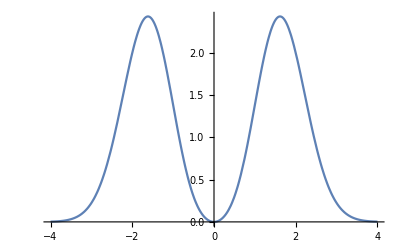

```mathematica
Plot[w[x], {x,-4,4}]
```

```mathematica
NIntegrate[w[x] (de[f][x])^2 /. param /. estimates, {x,-Infinity, Infinity}]
```

37.9818

```mathematica
NIntegrate[w[x] (de[f][x])^2 /. param /. {A->0.3, B->0.8}, {x,-Infinity, Infinity}]
```

54.9745

```mathematica
Plot3D[NIntegrate[w[x] (de[f][x])^2 /. param /. {A->a, B->b}, {x,-Infinity, Infinity}], {a, -1, 1}, {b,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[NIntegrate[w[x] (de[f][x])^2 /. param /. {A->a, B->b}, {x,-Infinity, Infinity}], {a, 0,2}, {b,0,2}]
```

-Graphics3D-

## Find minimum

```mathematica
criterion[a_,b_] :=NIntegrate[w[x] (de[f][x])^2 /. param /. {A->a, B->b}, {x,-Infinity, Infinity}];
```

```mathematica
vals = Table[criterion[a,b],{a,0.1, 2, 0.1},{b, 0.1, 2, 0.1}];
```

```mathematica
Min[vals]
```

1.93857

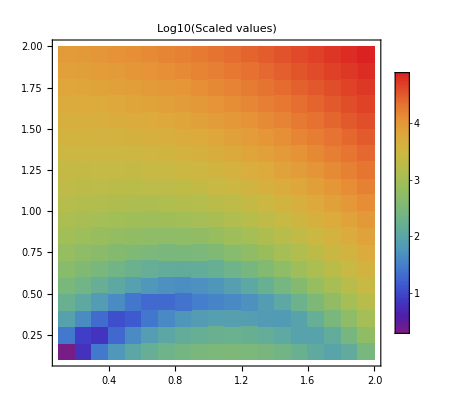

```mathematica
ListDensityPlot[Log10[vals], Mesh -> None, InterpolationOrder->0, PlotLegends->Automatic, DataRange->{{0.1, 2}, {0.1, 2}}, ColorFunction->"Rainbow", PlotLabel->"Log10(Scaled values)"]
```

Let’s scale these values by the amplitude^2:

```mathematica
valsscaled = vals / Table[(a+b)^2, {a, 0.1, 2, 0.1}, {b, 0.1, 2, 0.1}];
```

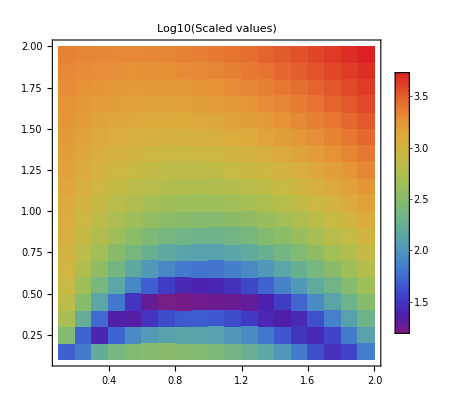

```mathematica
ListDensityPlot[Log10[valsscaled], Mesh -> None, InterpolationOrder->0, PlotLegends->Automatic, DataRange->{{0.1, 2}, {0.1, 2}}, ColorFunction->"Rainbow", PlotLabel->"Log10(Scaled values)"]
```

### Zoom in on the region

```mathematica
vals2 = Table[criterion[a,b] / (a+b)^2,{a,0.3, 0.5, 0.01},{b, 0.7, 1.2, 0.01}];
```

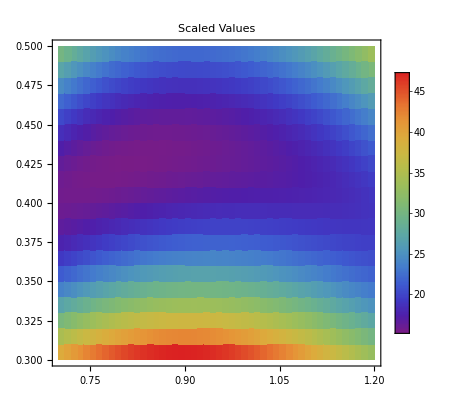

```mathematica
ListDensityPlot[vals2, Mesh -> None, InterpolationOrder->0, PlotLegends->Automatic, DataRange->{{0.7, 1.2}, {0.3, 0.5}}, ColorFunction->"Rainbow", PlotLabel->"Scaled Values"]
```

```mathematica
estimates
```

{A→0.445408,B→1.02817}

## New prior

```mathematica
criterion[a_,b_, w_] :=NIntegrate[w[x] (de[f][x] / (A  + B))^2 /. param /. {A->a, B->b}, {x,-Infinity, Infinity}];
```

```mathematica
w2[x_]:= If[Abs[x] < 0.1, 0, Exp[-x^2]]
```

```mathematica
w3[x_]:=Exp[-x^2] - Exp[-10x^2];
```

```mathematica
criterion[A /. estimates, B /. estimates, w3]
```

48.0104

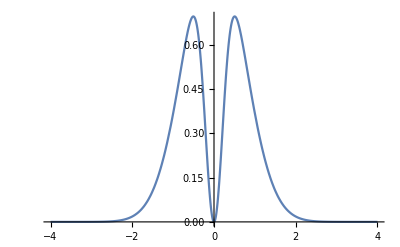

```mathematica
Plot[w3[x], {x,-4,4}]
```

```mathematica
vals3 = Table[criterion[a,b, w3] / (a+b)^2,{a,0.3, 0.5, 0.01},{b, 0.7, 1.2, 0.01}];
```

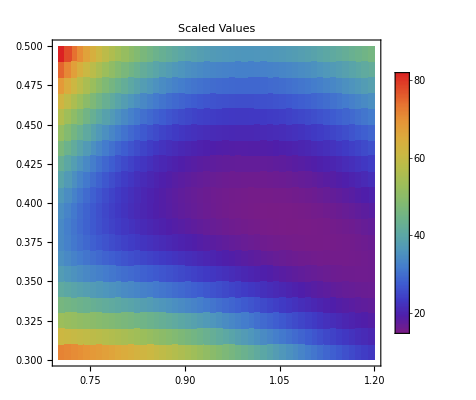

```mathematica
ListDensityPlot[vals3 , Mesh -> None, InterpolationOrder->0, PlotLegends->Automatic, DataRange->{{0.7, 1.2}, {0.3, 0.5}}, ColorFunction->"Rainbow", PlotLabel->"Scaled Values"]
```